```mathematica
colemanSpline[xx_]:=(
tx=xx;
For[i=1;tt={}; n=1,i≤Length[tx],i++;n++,
tt=Append[tt,{ {tx[[n,1]]},tx[[n,2]],tx[[n,3]]}];
];
finterp=Interpolation[tt];
ff[x_]:=(
n=Length[tx];
y=If[x<tx[[1,1]],tx[[1,3]] (x-tx [[1,1]])+tx[[1,2]],   If[x>=tx[[n,1]],tx[[n,3]] (x-tx [[n,1]])+tx[[n,2]],
finterp[x]]]

);
);
```

## NH4 Excretion -Graphics- EletrolyytesFLowConstant = 0.04 mmol/min = 57.6 mmol/d Spline: -Graphics- SplineLag: -Graphics- -Graphics-

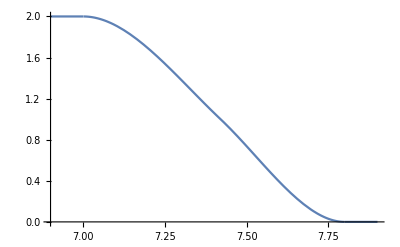

```mathematica
NH4Acute={{7.00,2.0,0},{7.42,1.0,-3.0},{7.80,0.0,0}};
(*           {{7.00,2.0,0},{7.45,1.0,-3.0},{7.80,0.0,0}} *)
colemanSpline[NH4Acute]
Plot[ff[pH],{pH,6.9,7.9}]
```

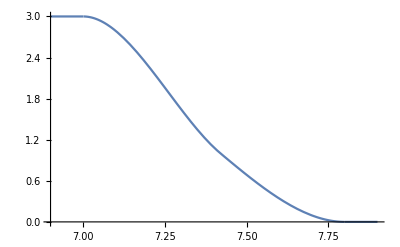

```mathematica
NH4Chronic={{7.00,3.0,0},{7.42,1.0,-4.0},{7.80,0.0,0}};
(*          {{7.00,3.0,0},{7.45,1.0,-4.0},{7.80,0.0,0}}    *)
colemanSpline[NH4Chronic]
Plot[ff[pH],{pH,6.9,7.9}]
```

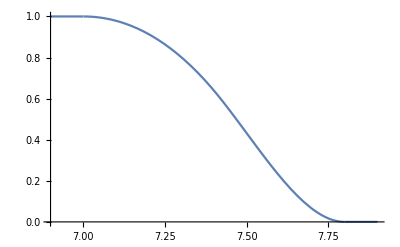

```mathematica
pHonFlux={{7.00,1.0,0},{7.42,0.6,-2.0},{7.80,0.0,0}};
(*       {{7.00,1.0,0},{7.45,0.6,-2.0},{7.80,0.0,0}} *)
colemanSpline[pHonFlux]
Plot[ff[pH],{pH,6.9,7.9}]
```

```mathematica
ff[7.2]
0.0674139*ff[7.2]
```

0.914048

0.0616196

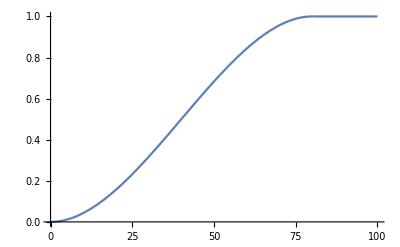

```mathematica
ChlorideEffect={{0.00,0.0,0},{80,1.0,0.0}};
colemanSpline[ChlorideEffect]
Plot[ff[pH],{pH,0,100}]
```

https://paperpile.com/shared/z8jfSE